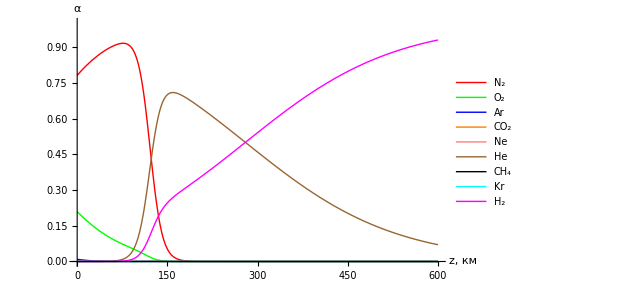

```mathematica
legend={"N_2", "O_2", "Ar", "CO_2", "Ne", "He", "CH_4", "Kr", "H_2"};
style={Directive[Red, Thick], Directive[Green, Thick], Directive[Blue, Thick], Directive[Orange, Thick], Directive[Pink, Thick], Directive[Brown, Thick], Directive[Black, Thick], Directive[Cyan, Thick], Directive[Magenta, Thick]};
alpha0={0.78074, 0.20946, 0.00934, 0.0004, 0.00001818, 0.00000524, 0.0000017, 0.0000014, 0.00000055};
m={28, 32, 40, 44, 20, 4, 16, 84, 2};
R = 8.31;
T=293;
g=9.81;
sumalpha[z_]:=Sum[alpha0[[i]]*Exp[-m[[i]]*g*z/R/T], {i, 1, Length[alpha0]}];
alpha[z_, i_]:=alpha0[[i]]*Exp[-m[[i]]*g*z/R/T]/sumalpha[z];
Plot[Evaluate@Table[alpha[x,n],{n,Length[alpha0]}], {x, 0,600}, PlotRange->{0,1}, PlotLegends->legend, PlotStyle->style,AxesLabel->{"z, км", "α"}]
```